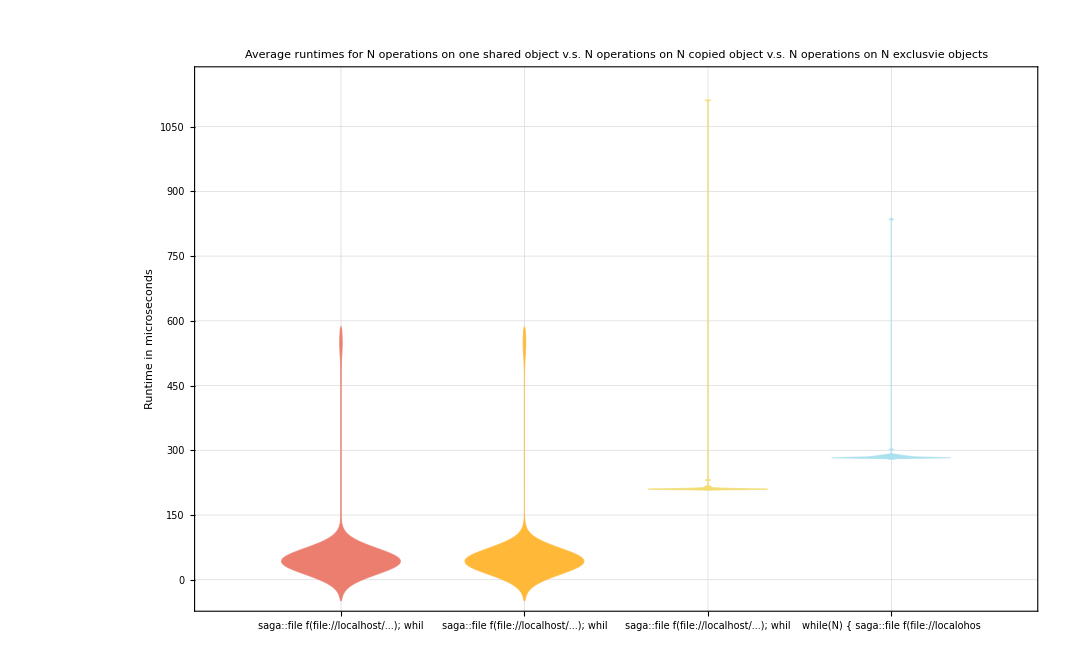

```mathematica
data= {
{(*data/run_d0_n1_stats*)ReadList[NotebookDirectory[] <> "./test_apiperf_02.dat"],
ReadList[NotebookDirectory[] <> "./test_apiperf_02.dat"],
ReadList[NotebookDirectory[] <> "./test_apiperf_03.dat"],
ReadList[NotebookDirectory[] <> "./test_apiperf_04.dat"]
}};

labels={
{"saga::file f(file://localhost/...); \nwhile(N) {f.op();}",
"saga::file f(file://localhost/...); \nwhile(N) {f_shalowcopy = f; f_shalowcopy.op();}",
"saga::file f(file://localhost/...); \nwhile(N) {f_deepcopy = f; f_deepcopy.op();}",
"while(N) { saga::file f(file://localohost/...); f.op();}" }};

DistributionChart[data,
ChartLabels -> labels, 
(*ChartElementFunction->"HistogramDensity",*)
ChartStyle->24,
FrameLabel->{"", "Runtime in microseconds"},
PlotLabel->"Average runtimes for N operations on one shared object v.s. N operations on N copied object v.s. N operations on N exclusvie objects",
GridLines->Automatic, GridLinesStyle->Directive[RGBColor[0.7,0.7,0.7], Dashed]
 ]
```